Cos[x]^2

{a_0→1,a_1→1/(4 π),a_2→-27/(2 π^2),a_3→18/π^3,a_4→0}

1+x/(4 π)-(27 x^2)/(2 π^2)+(18 x^3)/π^3

1+x/(4 π)-(27 x^2)/(2 π^2)+(18 x^3)/π^3

True

{True,True,True,True,True}

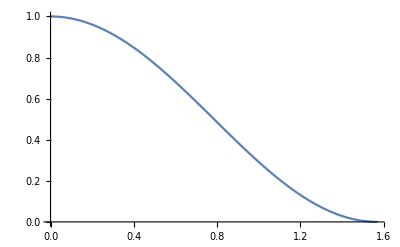

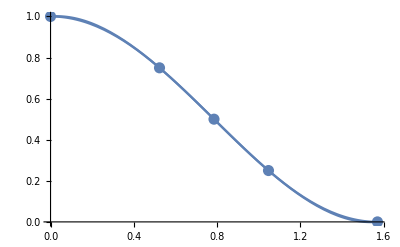

0.000937315

0.115336

```mathematica
f[x_]=Cos[x]^2
X={0,π/6, π/4, π/3, π/2};  F=f[X]; 

n=Length[X]-1;

Do[{Subscript[x, i]=X[[i+1]],Subscript[f, i]=F[[i+1]]},{i,0,n}]
koef=Solve[Table[Subscript[a, 0]+∑_(k=1)^n Subscript[a, k] Subscript[x, j]^k==Subscript[f, j],{j,0,n}],{}][[1]]
P[x_]=∑_(k=0)^n Subscript[a, k] x^k//.koef  //Expand
Tbl=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
P1[x_]=InterpolatingPolynomial[Tbl, x]//Expand 
P[x]==P1[x]
Table[P[Subscript[x, i]]==Subscript[f, i],{i,0,n}]
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Gr3 =Plot[Cos[x]^2,{x,0,π/2}]
Show[Gr1, Gr2,Gr3] 
x1=π/7;
ΔF=Abs[Cos[x1]^2-P[x1]]//N
δF=ΔF/P[x1]*100
```